# Vigenère Cipher

## Encryption

```mathematica
PlainText = ToLowerCase[StringDelete["MARKTWAINWASLAUDEDASTHEGREATESTHUMORISTTHEUNITEDSTATESHASPRODUCEDANDTHEFATHEROFAMERICANLITERATUREHISNOVELSINCLUDETHEADVENTURESOFTOMSAWYERANDITSSEQUELTHEADVENTURESOFHUCKLEBERRYFINNTHELATTEROFTENCALLEDTHEGREATAMERICANNOVELTWAINWASSERVEDANAPPRENTICESHIPWITHAPRINTERANDTHENWORKEDASATYPESETTERHEREFERREDHUMOROUSLYTOHISLACKOFSUCCESSATMININGHISHUMOROUSSTORYTHECELEBRATEDJUMPINGFROGOFCALAVERASCOUNTYBASEDONASTORYTHATHEHEARDATANGELSHOTELINANGELSCAMPCALIFORNIATHESHORTSTORYBROUGHTINTERNATIONALATTENTIONANDWASEVENTRANSLATEDINTOFRENCHHISWITANDSATIREINPROSEANDINSPEECHEARNEDPRAISEFROMCRITICSANDPEERSANDHEWASAFRIENDTOPRESIDENTSARTISTSINDUSTRIALISTSANDEUROPEANROYALTY", {PunctuationCharacter, WhitespaceCharacter}]];
PlainNums = LetterNumber[PlainText]-1;
lenP = Length[PlainNums];

CipherKey = ToUpperCase["twain"];
KeyNums = LetterNumber[CipherKey]-1;
lenK = Length[KeyNums];

CipherTxt = ToUpperCase[StringJoin[FromLetterNumber[Table[1+Mod[PlainNums[[i]]+KeyNums[[Mod[i, lenK, 1]]], 26],{i,1, lenP}]]]];

(* PRINT FUNCTIONS *)
Print[Style["Plain Text = \n", Bold, Gray], Style[PlainText,14, Blue, FontFamily->"Consolas"]];
Print[Style["Text Length = ", Bold, Gray], Style[lenP,16, Black, Bold]];
Print[Style["\nSecret Key = ", Bold, Gray], Style[CipherKey,16, Red, Bold], " → ", Style[KeyNums,14, Black, Italic]];
Print[Style["Key Length = ", Bold, Gray], Style[lenK,16, Red, Bold]];
Print[Style["\nCipher Text = \n", Bold, Gray], Style[CipherTxt,14, Red, FontFamily->"Consolas"]];
```

Plain Text = 
marktwainwaslaudedasthegreatesthumoristtheunitedstateshasproducedandthefatherofamericanliteraturehisnovelsincludetheadventuresoftomsawyeranditssequeltheadventuresofhuckleberryfinnthelatteroftencalledthegreatamericannoveltwainwasservedanapprenticeshipwithaprinterandthenworkedasatypesetterhereferredhumorouslytohislackofsuccessatmininghishumorousstorythecelebratedjumpingfrogofcalaverascountybasedonastorythatheheardatangelshotelinangelscampcaliforniatheshortstorybroughtinternationalattentionandwaseventranslatedintofrenchhiswitandsatireinproseandinspeechearnedpraisefromcriticsandpeersandhewasafriendtopresidentsartistsindustrialistsandeuropeanroyalty

Text Length = 652

Secret Key = TWAIN → {19,22,0,8,13}

Key Length = 5

Cipher Text = 
FWRSGPWIVJTOLIHWADIFMDEOEXWTMFMDUUBKESBGAAUVVMADAGTPEAUTOPZBWQCMQTJDBUXBABUXNONNFARQPTJLQGXNABHKAHQFGKVMYLENKYNZEBUXWDDRGPUZRLKFBBFOAELXNAVQBPSARJQETGAAALIXJTCEXOONUNYKTRUARZLYENVGAALIGMARWSMANKNEHELGAAGZRTPAURKECIAGKVMYMSAQAPWSARKRELNGWPXEXJTQPXOHQCPETPNINIVGXNAVQMDEVJHNKMQTOABLIASMGMARPRKAFMEKADPHFKRWHLHYBBAESTNVGONFNYCMFLWTUVGENOUBOHCZHNOCFLPOZLMDEKREABZNMADRHFLIVTYNOOBYYATNOARIFVKUVGRXAARWKNIFMKRGGAWTPRAAAZQTPAVTXHSPBMALQATJGMYLYAUCVWLQSHNNQNMDEAUHNTAGHNYJEHQGPGBJTMEGWTQBGWLIGMANBVHJAVQPWSMIXJTZNGOLIGXZIVGHBRMAVDHQFPETIAWOABVKAIVCKKSMNGZIVFIAEKUXWRVRWLRIVLAFZBFYRQGBYSIAWLEMELWNLUXSAANYNIMAWPOXEXOILRGPSIEMESBFBJDCFMNIIYBOTANGZECEHLEIAKKYIYMU

## Cryptanalysis

### Frequency Table

Function to get frequency of a letter using a number {1->"A" ... 26->"Z"}

Cipher Text = 
FWRSGPWIVJTOLIHWADIFMDEOEXWTMFMDUUBKESBGAAUVVMADAGTPEAUTOPZBWQCMQTJDBUXBABUXNONNFARQPTJLQGXNABHKAHQFGKVMYLENKYNZEBUXWDDRGPUZRLKFBBFOAELXNAVQBPSARJQETGAAALIXJTCEXOONUNYKTRUARZLYENVGAALIGMARWSMANKNEHELGAAGZRTPAURKECIAGKVMYMSAQAPWSARKRELNGWPXEXJTQPXOHQCPETPNINIVGXNAVQMDEVJHNKMQTOABLIASMGMARPRKAFMEKADPHFKRWHLHYBBAESTNVGONFNYCMFLWTUVGENOUBOHCZHNOCFLPOZLMDEKREABZNMADRHFLIVTYNOOBYYATNOARIFVKUVGRXAARWKNIFMKRGGAWTPRAAAZQTPAVTXHSPBMALQATJGMYLYAUCVWLQSHNNQNMDEAUHNTAGHNYJEHQGPGBJTMEGWTQBGWLIGMANBVHJAVQPWSMIXJTZNGOLIGXZIVGHBRMAVDHQFPETIAWOABVKAIVCKKSMNGZIVFIAEKUXWRVRWLRIVLAFZBFYRQGBYSIAWLEMELWNLUXSAANYNIMAWPOXEXOILRGPSIEMESBFBJDCFMNIIYBOTANGZECEHLEIAKKYIYMU

FREQUENCY TABLE

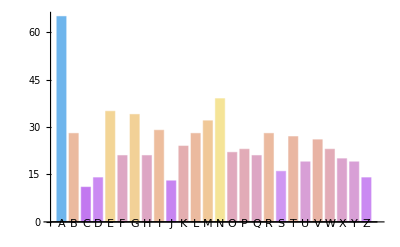

A | N | E | G | M | I | B | L | R | T | V | K | P | W | O | Q | H | F | X | Y | U | S | Z | D | J | C
65 | 39 | 35 | 34 | 32 | 29 | 28 | 28 | 28 | 27 | 26 | 24 | 23 | 23 | 22 | 21 | 21 | 21 | 20 | 19 | 19 | 16 | 14 | 14 | 13 | 11

```mathematica
(* CenterDot@@(Superscript@@@FactorInteger[lenC]); *)
ct1 ="FWRSGPWIVJTOLIHWADIFMDEOEXWTMFMDUUBKESBGAAUVVMADAGTPEAUTOPZBWQCMQTJDBUXBABUXNONNFARQPTJLQGXNABHKAHQFGKVMYLENKYNZEBUXWDDRGPUZRLKFBBFOAELXNAVQBPSARJQETGAAALIXJTCEXOONUNYKTRUARZLYENVGAALIGMARWSMANKNEHELGAAGZRTPAURKECIAGKVMYMSAQAPWSARKRELNGWPXEXJTQPXOHQCPETPNINIVGXNAVQMDEVJHNKMQTOABLIASMGMARPRKAFMEKADPHFKRWHLHYBBAESTNVGONFNYCMFLWTUVGENOUBOHCZHNOCFLPOZLMDEKREABZNMADRHFLIVTYNOOBYYATNOARIFVKUVGRXAARWKNIFMKRGGAWTPRAAAZQTPAVTXHSPBMALQATJGMYLYAUCVWLQSHNNQNMDEAUHNTAGHNYJEHQGPGBJTMEGWTQBGWLIGMANBVHJAVQPWSMIXJTZNGOLIGXZIVGHBRMAVDHQFPETIAWOABVKAIVCKKSMNGZIVFIAEKUXWRVRWLRIVLAFZBFYRQGBYSIAWLEMELWNLUXSAANYNIMAWPOXEXOILRGPSIEMESBFBJDCFMNIIYBOTANGZECEHLEIAKKYIYMU";

CipherTxt = ToUpperCase[StringDelete[ct1,{PunctuationCharacter,WhitespaceCharacter}]];
vcFreq = LetterCounts[CipherTxt];
vcFreqAlpha = Association[SortBy[Normal[vcFreq], First]];

Print[Style["\nCipher Text = \n", Bold, Gray], Style[CipherTxt,14, Red, FontFamily->"Consolas"]];
Print[Style["\nFREQUENCY TABLE", 14,Bold, Gray]];

BarChart[vcFreqAlpha, ChartLabels->Automatic, ColorFunction->"Pastel"]
Grid[Transpose[List @@@ Normal[vcFreq]], Frame->All]
```

### Kaisiski Test

#### Support Functions

```mathematica
(*Function to split string into n columns*)
splitStr = Function[{str,num},Map[StringJoin,Transpose[Partition[Characters[str], num]]]];
(*Function to get the frequency count of enumerated letter*)
freqi = Function[{freq, i}, Lookup[freq, ToUpperCase[FromLetterNumber[i]], 0]];
(*Function to calculate IC given a frequency table*)
calcIC = Function[{freq}, Sum[freqi[freq,i]*(freqi[freq,i]-1)/(Total[freq]*(Total[freq]-1)),{i,1,26}]];
(*Function to caesar shift the string by a given key*)
caesarShiftCol = Function[{ctext,shift},ToUpperCase[StringJoin[FromLetterNumber[Mod[LetterNumber[ctext]-1+shift,26,1]]]]];
```

#### Key Length

KEYLENGTH vs IoC

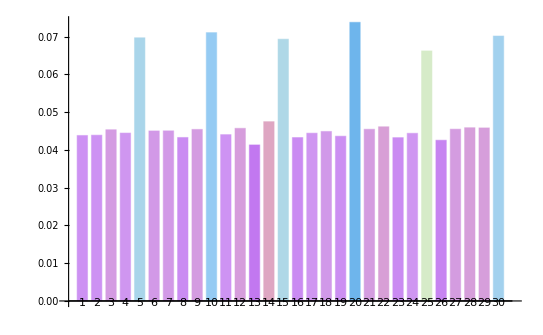

Probable Key Length = 5

```mathematica
keyLenFreq = Association[];

For[kn=1,kn≤30,kn++,
textGroups = splitStr[CipherTxt, kn];
freqGroups = Table[LetterCounts[textGroups[[i]]], {i, 1, Length[textGroups]}];
kIC = N[Sum[calcIC[freqGroups[[k]]]/Length[textGroups],{k,1,Length[textGroups]}]];
AppendTo[keyLenFreq, kn->kIC];
]

(* PRINT FUNCTIONS *)
Print[Style["\nKEYLENGTH vs IoC", 14,Bold, Gray]];
BarChart[keyLenFreq, ChartLabels->Automatic, ColorFunction->"Pastel"]

gcdKey = GCD @@ Keys[TakeLargestBy[keyLenFreq, Identity, 5]];
Print[Style["Probable Key Length = ", Bold, Gray], Style[gcdKey,16, Red, Bold]];
```

### Brute Force with Key Length

#### Possible Dictionary Words as Keys

```mathematica
(*Function to Decrypt Vigenere encrypted Text, with the provided Key*)
decryptVigenere = Function[{encNums,kNums},ToLowerCase[StringJoin[FromLetterNumber[Table[1+Mod[encNums[[i]]-kNums[[Mod[i, Length[kNums], 1]]], 26],{i,1, Length[encNums]}]]]]];
(*Find all words from the dictionary with length=KeyLength*)
possibleWords = LetterNumber[ToUpperCase[Select[DictionaryLookup["*"],StringLength[#]==gcdKey&]]];
lenPossW = Length[possibleWords];
ctTxt = LetterNumber[StringTake[CipherTxt, 3*gcdKey]];

Print[Style["\nTotal Word Combinations = ", Bold, Gray], Style[lenPossW,14, Red, FontFamily->"Consolas"]];
Print[Style["Shortened Test Cipher Text = ", Bold, Gray], Style[StringTake[CipherTxt,2*gcdKey],14, Red, FontFamily->"Consolas"], " → ", Style[ctTxt,14, Black, Italic]];
```

Total Word Combinations = 6789

Shortened Test Cipher Text = FWRSGPWIVJ → {6,23,18,19,7,16,23,9,22,10,20,15,12,9,8}

#### Brute Force Decryption

```mathematica
(*Check if the strings are parts of English words*)
isDictQ = Function[{word},DictionaryWordQ[StringTake[word,4]]];
bruteDecrypt =Table[decryptVigenere[ctTxt, possibleWords[[kkn]]],{kkn,1,lenPossW}];

Select[bruteDecrypt, isDictQ]
```

{fraeoprrhrtjuup,ewesvowvvysoyiw,dikeonibhrraeup,digsonixvrraaip,diestnivvwrayiu,didodniurgraxee,diamynirpbraucz,diagonirjrrauwp,cohoomoyrrqgbep,cocasmotdvqgwqt,cowstmonvwqgqiu,cowsomonvrqgqip,costimojwlqgmjj,bugsnluxvqpmaio,bollnlocoqpgfbo,blaeillrhlpduuj,aspsvksgvyokjiw,woksdgobvgkgeie,woestgovvwkgyiu,twosudwfvxhoiiv,tweepdwvhshoyuq,twasndwrvqhouio,topszdogvchgjia,topiidogllhgjyj,tookodofnrhgiap,tollndocoqhgfbo,togstdoxvwhgaiu,toeawdovdzhgyqx,tosspdojvshgmiq,tipiodiglrhajyp,solovcocryggfew,solopcocrsggfeq,soukccolnfggoad,sinhociekrgahxp,sinhociekrgahxp,singyciejbgahwz,runstbuevwfmhiu,repspbegvsfwjiq,refstbewvwfwziu,owlsoywcvrcofip,oilycyicbfcafod,nuderxuuhubmxus,nudenxuuhqbmxuo,noesyxovvbbgyiz,narktxainwbslau,nardoxaigrbsltp,nanspxaevsbshiq,nansnxaevqbshio,nanorxaerubshes,nanonxaerqbsheo,nanonxaerqbsheo,nandnxaegqbshto,moosvwofvyagiiw,mollnwocoqagfbo,mostiwojwlagmjj,milsowicvraafip,micshwitvkaawii,mickewitnhaawaf,micaiwitdlaawqj,marktwainwaslau,marktwainwaslau,manswwaevzashix,kipsvuigvyyajiw}

```mathematica
selectTxt = "marktwainwaslau";
selectShifts = StringTake[StringJoin[FromLetterNumber[Mod[ctTxt+1 - LetterNumber[selectTxt],26,1]]],gcdKey];

decryptTrial = decryptVigenere[LetterNumber[CipherTxt],LetterNumber[selectShifts]];

Print[Style["Possible Keyword = ", Bold, Gray], Style[selectShifts,14, Blue, FontFamily->"Consolas"], " → ", Style[LetterNumber[selectShifts],14, Black, Italic]];
Print[Style["\nDecrypted Text = \n", Bold, Gray], Style[decryptTrial,14, Purple, FontFamily->"Consolas"]];
```

Possible Keyword = twain → {20,23,1,9,14}

Decrypted Text = 
marktwainwaslaudedasthegreatesthumoristtheunitedstateshasproducedandthefatherofamericanliteraturehisnovelsincludetheadventuresoftomsawyeranditssequeltheadventuresofhuckleberryfinnthelatteroftencalledthegreatamericannoveltwainwasservedanapprenticeshipwithaprinterandthenworkedasatypesetterhereferredhumorouslytohislackofsuccessatmininghishumorousstorythecelebratedjumpingfrogofcalaverascountybasedonastorythatheheardatangelshotelinangelscampcaliforniatheshortstorybroughtinternationalattentionandwaseventranslatedintofrenchhiswitandsatireinproseandinspeechearnedpraisefromcriticsandpeersandhewasafriendtopresidentsartistsindustrialistsandeuropeanroyalty

#### Frequency Analysis of Columns

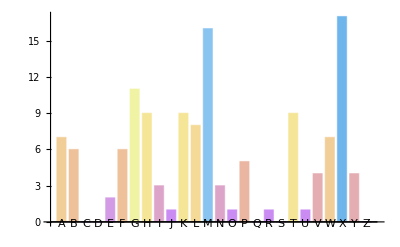
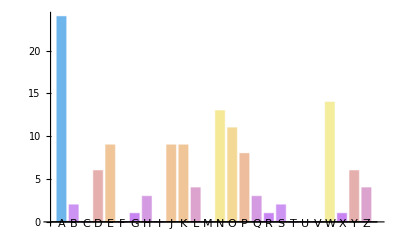
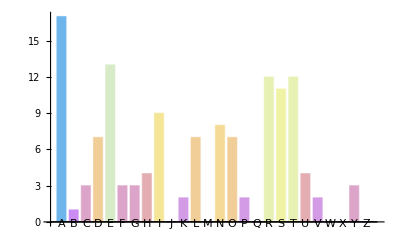
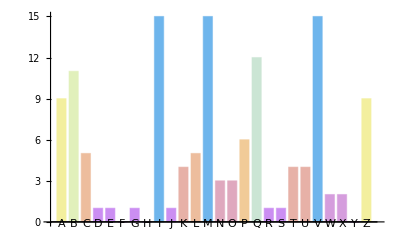
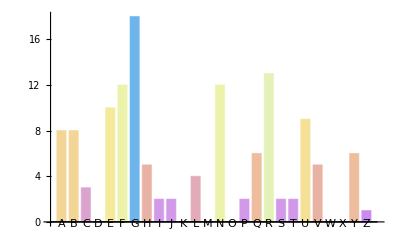

```mathematica
alpha = "ABCDEFGHIJKLMNOPQRSTUVWXYZ";
scTxt = splitStr[CipherTxt, gcdKey];
scTxtFreq = Table[LetterCounts[StringJoin[scTxt[[s]],alpha]]-1, {s,1,Length[scTxt]}];
Table[BarChart[Association[SortBy[Normal[scTxtFreq[[ss]]],First]],ChartLabels->Automatic,ColorFunction->"Pastel"],{ss,1,Length[scTxt]}]
```